```mathematica
(*Question 1a*)
Limit[Coth[1/(2J)x],J->∞]
```

DirectedInfinity[1/Sign[x]]

```mathematica
Limit[Sinh[1/(2J)x],J->∞]
```

0

```mathematica
(*Question 1b*)
Series[(2J+1)/(2J)Coth[(2J+1)/(2J)x]-1/(2J)Coth[1/(2J)x],{x,0,2}]
```

((1+J) x)/(3 J)+O[x]^3

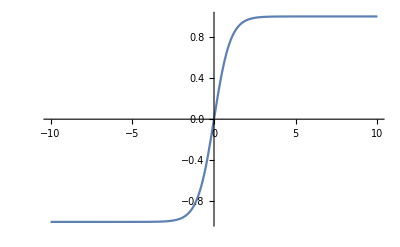

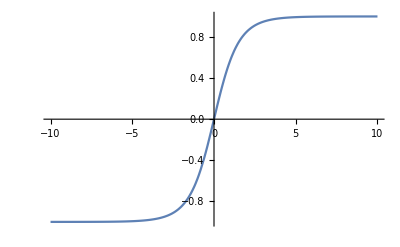

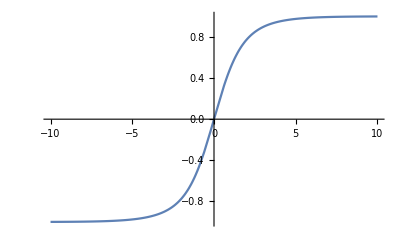

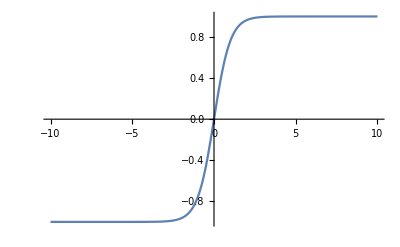

```mathematica
(*Question 1c*)
BJ[J_,a_]:=(2J+1)/(2J)Coth[(2J+1)/(2J)a]-1/(2J)Coth[1/(2J)a]
Plot[BJ[1/2,a],{a,-10,10}]
Plot[BJ[1,a],{a,-10,10}]
Plot[BJ[3/2,a],{a,-10,10}]
Plot[Tanh[x],{x,-10,10}]
```

```mathematica
(*Question 1d*)
D[Tanh[(g*muB*mu0*(H+lam*m))/(2kB*T)],H]
```

(g mu0 muB Sech[(g (H+lam m) mu0 muB)/(2 kB T)]^2)/(2 kB T)

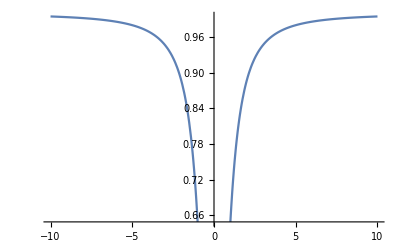

```mathematica
Plot[Sech[1/T],{T,-10,10}]
```

0

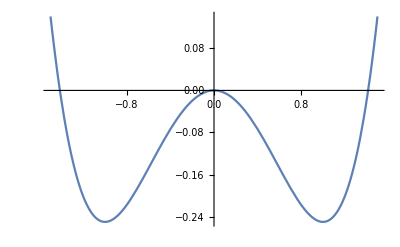

0.5

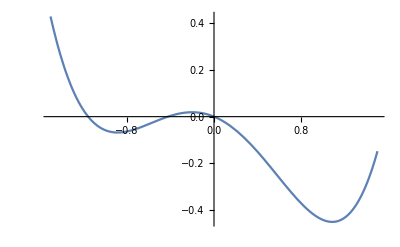

1.2

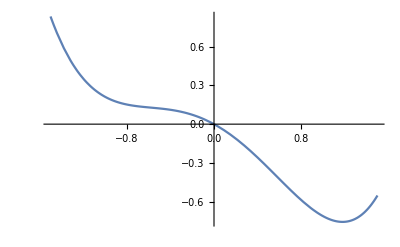

```mathematica
(*Question 2c*)
e=0
Plot[-1/2 p^2+1/4 p^4-2/(3 √3)p*e,{p,-1.5,1.5}]
e=0.5
Plot[-1/2 p^2+1/4 p^4-2/(3 √3)p*e,{p,-1.5,1.5}]
e=1.2
Plot[-1/2 p^2+1/4 p^4-2/(3 √3)p*e,{p,-1.5,1.5}]
```

```mathematica
(*Question 2e*)
Clear["Global`*"]
f[p_]:=1/4 p^4-1/2 p^2-(2e)/(3 √3)p
FullSimplify[Solve[D[f[p],p]==0,p]]
D[D[f[p],p],p]
fpp[p_]:=-1+3 p^2
```

{{p→(1+(e+√(-1+e^2))^(2/3))/(√3 (e+√(-1+e^2))^(1/3))},{p→(-3 ⅈ-√3+3 ⅈ (e+√(-1+e^2))^(2/3)-√3 (e+√(-1+e^2))^(2/3))/(6 (e+√(-1+e^2))^(1/3))},{p→(3 ⅈ-√3-3 ⅈ (e+√(-1+e^2))^(2/3)-√3 (e+√(-1+e^2))^(2/3))/(6 (e+√(-1+e^2))^(1/3))}}

-1+3 p^2

```mathematica
fpp[(1+(e+√(-1+e^2))^(2/3))/(√3 (e+√(-1+e^2))^(1/3))]/.e->1
fpp[(-3 ⅈ-√3+3 ⅈ (e+√(-1+e^2))^(2/3)-√3 (e+√(-1+e^2))^(2/3))/(6 (e+√(-1+e^2))^(1/3))]/.e->1
fpp[(3 ⅈ-√3-3 ⅈ (e+√(-1+e^2))^(2/3)-√3 (e+√(-1+e^2))^(2/3))/(6 (e+√(-1+e^2))^(1/3))]/.e->1
```

3

0

0

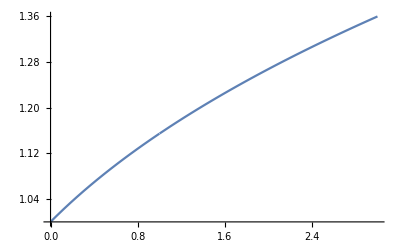

```mathematica
Plot[(1+(e+√(-1+e^2))^(2/3))/(√3 (e+√(-1+e^2))^(1/3)),{e,0,3}]
```

-0.0440424-0.519686 ⅈ

-0.0440424+0.519686 ⅈ

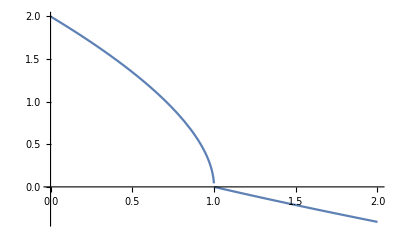

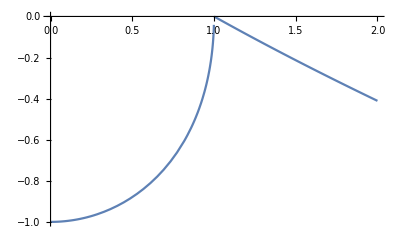

```mathematica
fpp[(-3 ⅈ-√3+3 ⅈ (e+√(-1+e^2))^(2/3)-√3 (e+√(-1+e^2))^(2/3))/(6 (e+√(-1+e^2))^(1/3))/.e->1.1]
fpp[(3 ⅈ-√3-3 ⅈ (e+√(-1+e^2))^(2/3)-√3 (e+√(-1+e^2))^(2/3))/(6 (e+√(-1+e^2))^(1/3))/.e->1.1]
Plot[Re[fpp[(-3 ⅈ-√3+3 ⅈ (e+√(-1+e^2))^(2/3)-√3 (e+√(-1+e^2))^(2/3))/(6 (e+√(-1+e^2))^(1/3))]],{e,0,2}]
Plot[Re[fpp[(3 ⅈ-√3-3 ⅈ (e+√(-1+e^2))^(2/3)-√3 (e+√(-1+e^2))^(2/3))/(6 (e+√(-1+e^2))^(1/3))]],{e,0,2}]
```

```mathematica
(*Question 2f*)
```

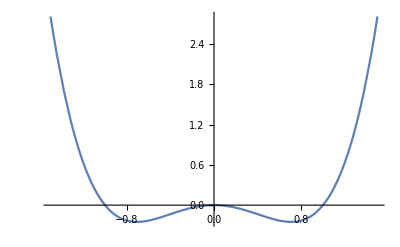

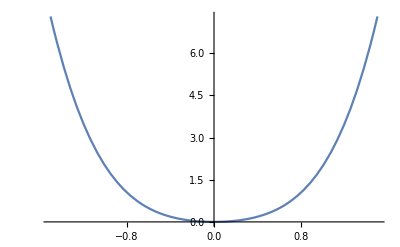

```mathematica
(*Question 4*)
Plot[x^4-x^2,{x,-1.5,1.5}]
Plot[x^4+x^2,{x,-1.5,1.5}]
```

```mathematica
FullSimplify[1/2 beta*((alpha(1-t)^2)/beta)^2+alpha*(t-1)*(alpha*(1-t))/beta]
```

(alpha^2 (-1+t)^2 (-1+(-2+t) t))/(2 beta)

```mathematica
Expand[alpha^2 (-1+t)^2 (-1+(-2+t) t)]/(2 beta)
```

(-alpha^2+4 alpha^2 t^2-4 alpha^2 t^3+alpha^2 t^4)/(2 beta)

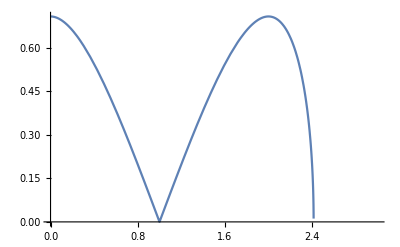

```mathematica
Plot[Sqrt[-1(-alpha^2/(2 beta)+(2 alpha^2 t^2)/beta-(2 alpha^2 t^3)/beta+(alpha^2 t^4)/(2 beta))]/.{alpha->1,beta->1},{t,0,3}]
```

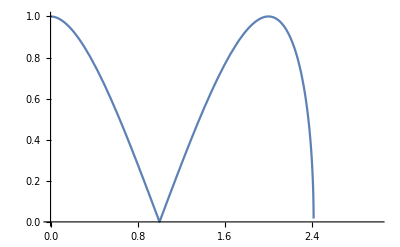

```mathematica
Plot[√(-1(t-1)^2(t^2-2t-1)),{t,0,3}]
```